```mathematica
(*parameter t at point p when p is local maximum curvature point*)
maxParam[{c0_,p_,c2_},w_:1]:=NSolve[(-(1-t)^2(c0-p)+t^2(c2-p)).(((1-t)t+w(1-t)^2)(c0-p)+((1-t)t+w t^2)(c2-p))==0&&0≤t≤1,t,Reals]⟦1,1,2⟧//N

area[{a_,b_,c_}]:=Abs[Det[{b-a,c-b}]/2]

(*the interpolation coefficient of the joint points*)
lambda[{c0_,c1_,c3_,c4_},{w1_:1,w3_:1}]:=(√area[{c0,c1,c3}]/w1)/(√area[{c0,c1,c3}]/w1+√area[{c1,c3,c4}]/w3)//N

(*weight functions*)
minEccWeight[{c0_,c1_,c2_}]:=√(((c0-c2).(c0-c2))/(2((c0-c1).(c0-c1)+(c2-c1).(c2-c1))))
clampedME[{c0_,c1_,c2_}]:=Max[.5,minEccWeight[{c0,c1,c2}]]

(*closed rational κCurve from given input points. pts must be at least three points*)
rationalClosed[pts_, weightFunc_:clampedME,iterations_:30]:=Module[{n=Length[pts],ctrls,w,t,λ,mat},
(*control points of the bezier control polygon*)
ctrls=Table[{(pts⟦i⟧+pts⟦Mod[i-1,n,1]⟧)/2,pts⟦i⟧,(pts⟦i⟧+pts⟦Mod[i+1,n,1]⟧)/2},{i,n}];

Do[w=Table[weightFunc[ctrls⟦i⟧],{i,n}];
t=Table[maxParam[{ctrls⟦i,1⟧,pts⟦i⟧,ctrls⟦i,3⟧},w⟦i⟧],{i,n}];
λ=Table[lambda[Join[ctrls⟦i,{1,2}⟧,ctrls⟦Mod[i+1,n,1],{2,3}⟧],w⟦{i,Mod[i+1,n,1]}⟧],{i,n}];

mat=Table[0,n,n];
Do[mat⟦i,{Mod[i-1,n,1],i,Mod[i+1,n,1]}⟧={((1-λ⟦Mod[i-1,n,1]⟧)(1-t⟦i⟧)^2)/((1-t⟦i⟧)^2+w⟦i⟧2(1-t⟦i⟧)t⟦i⟧+t⟦i⟧^2),(λ⟦Mod[i-1,n,1]⟧(1-t⟦i⟧)^2+w⟦i⟧2(1-t⟦i⟧)t⟦i⟧+(1-λ⟦i⟧)t⟦i⟧^2)/((1-t⟦i⟧)^2+w⟦i⟧2(1-t⟦i⟧)t⟦i⟧+t⟦i⟧^2),(λ⟦i⟧t⟦i⟧^2)/((1-t⟦i⟧)^2+w⟦i⟧2(1-t⟦i⟧)t⟦i⟧+t⟦i⟧^2)},{i,n}];

(*off-curve Bezier control points*)
ctrls⟦All,2⟧=Inverse[mat].pts;
(*joint points between quadratic segments*)
Do[ctrls⟦Mod[i+1,n,1],1⟧=ctrls⟦i,3⟧=(1-λ⟦i⟧)ctrls⟦i,2⟧+λ⟦i⟧ctrls⟦Mod[i+1,n,1],2⟧,{i,n}],

iterations(*30 by default*)];
{ctrls,w}
]

(* open rational κCurve from given input points. pts must be at least three points*)
rationalOpen[pts_,weightFunc_:clampedME, iterations_:30]:=Module[{n=Length[pts]-2,ctrls,w,t,λ,matA,matB},
(*control points of the bezier control polygon*)
ctrls=Table[{(pts⟦i⟧+pts⟦i-1⟧)/2,pts⟦i⟧,(pts⟦i⟧+pts⟦i+1⟧)/2},{i,2,Length[pts]-1}];
(*the two end points will be used as constants*)
ctrls⟦1,1⟧=pts⟦1⟧;
ctrls⟦-1,-1⟧=pts⟦-1⟧;

Do[w=Table[weightFunc[ctrls⟦i⟧],{i,n}];
t=Table[maxParam[{ctrls⟦i,1⟧,pts⟦i+1⟧,ctrls⟦i,3⟧},w⟦i⟧],{i,n}];
λ=Table[lambda[Join[ctrls⟦i,{1,2}⟧,ctrls⟦i+1,{2,3}⟧],w⟦{i,Mod[i+1,n,1]}⟧],{i,n-1}];

(*tridiagonal matrix A*)
matA=DiagonalMatrix[Table[(w⟦i⟧2(1-t⟦i⟧)t⟦i⟧)/((1-t⟦i⟧)^2+w⟦i⟧2(1-t⟦i⟧)t⟦i⟧+t⟦i⟧^2),{i,n}]];
Do[matA⟦i,{i,i+1}⟧+=({1-λ⟦i⟧,λ⟦i⟧}t⟦i⟧^2)/((1-t⟦i⟧)^2+w⟦i⟧2(1-t⟦i⟧)t⟦i⟧+t⟦i⟧^2),{i,n-1}];
Do[matA⟦i,{i-1,i}⟧+=({1-λ⟦i-1⟧,λ⟦i-1⟧}(1-t⟦i⟧)^2)/((1-t⟦i⟧)^2+w⟦i⟧2(1-t⟦i⟧)t⟦i⟧+t⟦i⟧^2),{i,2,n}];
(*two end points are constants*)
matB=pts⟦2;;-2⟧;
matB⟦1⟧-=(1-t⟦1⟧)^2/((1-t⟦1⟧)^2+w⟦1⟧2(1-t⟦1⟧)t⟦1⟧+t⟦1⟧^2)pts⟦1⟧;
matB⟦-1⟧-=t⟦-1⟧^2/((1-t⟦-1⟧)^2+w⟦-1⟧2(1-t⟦-1⟧)t⟦-1⟧+t⟦-1⟧^2)pts⟦-1⟧;

(*off-curve Bezier control points*)
ctrls⟦All,2⟧=Inverse[matA].matB;
(*joint points between quadratic segments*)
Do[ctrls⟦i+1,1⟧=ctrls⟦i,3⟧=(1-λ⟦i⟧)ctrls⟦i,2⟧+λ⟦i⟧ctrls⟦i+1,2⟧,{i,n-1}],

iterations(*30 by default*)];
{ctrls,w}
]
(*Rendering*)
RationalBezierCurve[{ctrls_,ws_}]:=Line[Table[((1-t)^2 ctrls⟦i,1⟧+ws⟦i⟧ 2(1-t)t ctrls⟦i,2⟧+t^2 ctrls⟦i,3⟧)/((1-t)^2+ws⟦i⟧ 2(1-t)t+t^2),{i,Length[ws]},{t,0,1,.01}]]
```

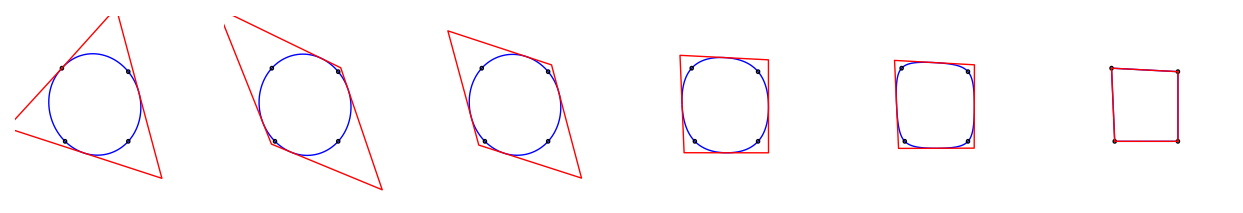

```mathematica
input={{-2.2,2.2},{2,2},{2,-2},{-2,-2}};
GraphicsRow[Table[Graphics[{Blue,RationalBezierCurve[#],Black,Table[Circle[pt,.1],{pt,input}],Red,Line[#⟦1⟧]}&[rationalClosed[input,func]],PlotRange->{{-5,5},{-5,5}}],{func,{.5&,minEccWeight,clampedME,1&,2&,1000&}}]]
```

```mathematica
Manipulate[Graphics[RationalBezierCurve[rationalClosed[pts]],PlotRange->{{-5,5},{-5,5}}],{{pts,{{-1,1},{1,1},{1,-1},{-1,-1}}},Locator}]
```

```mathematica
Manipulate[Graphics[RationalBezierCurve[rationalOpen[pts]],PlotRange->{{-5,5},{-5,5}}],{{pts,{{-1,1},{1,1},{1,-1},{-1,-1}}},Locator}]
```